# Въведение

```mathematica
v = {4,4.5,-9,4,3}
```

{4,4.5,-9,4,3}

```mathematica
sin
```

sin

```mathematica
Sin
```

```mathematica
Sin[v]
```

{Sin[4],-0.97753,-Sin[9],Sin[4],Sin[3]}

пиша текст с Alt + 7

пояснение за действия със списъци

```mathematica
vv = {4.0,4.5,-9.,4.,3.}(* въвеждане на списък от числа *)
Sin[vv]
```

{4.,4.5,-9.,4.,3.}

{-0.756802,-0.97753,-0.412118,-0.756802,0.14112}

```mathematica
-0.7568024953079282
```

# КЧМ за решаване на нелинейни уравнения

Задача: Да се реши уравнението (1. Да се намери броя на корените, 2. Да се уточни най-малкия корен)
		x^3+45cos x + 6x -76 = 0

## Графично представяне на функцията

### Дефиниция на функция

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
```

### Графика на функция

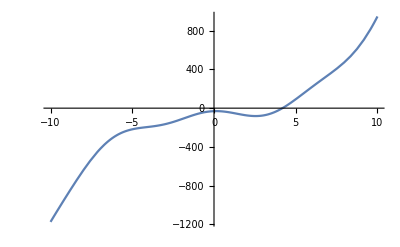

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Plot[function,{var,min,max}]
```

Извод: Уравнението има един корен.

## Локализация на корен

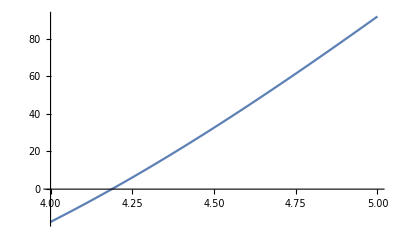

```mathematica
Plot[f[x],{x,4,5}]
```

```mathematica
f[4]
```

12+45 Cos[4]

```mathematica
f[4.]
```

-17.414

```mathematica
f[5.]
```

91.7648

или

```mathematica
f[4.]*f[5.]
```

-1597.99

Извод:
Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции (полиним и косинус). 
f(4) = -17.4... < 0
f(5) = 91.76... > 0
Функцията има различни знаци в двата края на разглеждания интервал [4; 5]. 
Следователно  в този интервал [4; 5] функцията има корен.

## Уточняване на корен

## Оценка на грешката